Distance Measures between Quantum States

Norms and Distancespaclet:QuantumMob/Q3/tutorial/DistanceMeasuresBetweenQuantumStates#1279618553 | Hilbert-Schmidt and Trace Distancespaclet:QuantumMob/Q3/tutorial/DistanceMeasuresBetweenQuantumStates#1523037456
Hilbert-Schmidt and Trace Normspaclet:QuantumMob/Q3/tutorial/DistanceMeasuresBetweenQuantumStates#1933235710 | Fidelitypaclet:QuantumMob/Q3/tutorial/DistanceMeasuresBetweenQuantumStates#710264195

See also Section 5.5 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

A distance measure quantifies the extent to which two quantum states share similar characteristics. Quantum states undergo various operations, unitary or non-unitary, intended or incidental. It is inevitable to quantitatively compare the quantum states before and after those operations to assess their effects.

In general,  While these distance measures are usually given by certain mathematical expressions, they often possess a simple operational meaning, i.e., they are related to the problem of distinguishing two systems.

There are various ways of introducing a notion of distance between two quantum states. Here we introduce three methods of quantifying how close two quantum states are. The first two, the Hilbert-Schmidt and trace distances, are metrics, a mathematical notion of “distance”. It sounds natural to say that two states are closer when the distance between them are smaller. The third, fidelity, is conceptually a relative angle. Since quantum states are normalized, it seems reasonable to regard two quantum states closer when the relative angle is smaller. Fidelity is not a metric in the precise mathematical sense and yet well describes the “closeness” of quantum states in many respects. Distance measures often possess a simple operational meaning, and depending on the protocol or system in question, one measure is favored operationally than others.

In quantum information, the trace distance appears far more frequently than the Hilbert-Schmidt distance. One possible reason is that the classical version of trace distance is widely used in statistics. However, there seems to be no profound reason to prefer one to the other in general. Both share many properties in common. One is more convenient in one situation but less in others. It is also heuristic to compare them closely with one another.

HilbertSchmidtDistancepaclet:QuantumMob/Q3/ref/HilbertSchmidtDistanceQuantumMob Package Symbol | The Hilbert-Schmidt distance between two quantum states.
TraceDistancepaclet:QuantumMob/Q3/ref/TraceDistanceQuantumMob Package Symbol | The trace distance between two quantum states.
Fidelitypaclet:QuantumMob/Q3/ref/FidelityQuantumMob Package Symbol | The fidelity between two quantum states.
Supermappaclet:QuantumMob/Q3/ref/SupermapQuantumMob Package Symbol | Represents a supermap.

Q3 functions useful for distance measures between two quantum states.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
Needs["QuantumMob`Q3`"]
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Norms and Distances

Before we discuss the two metric-based closeness measures, we first recall the relation between Hermitian product, norm, and distance. It will serve as an outline for our discussions on the Hilbert-Schmidt and trace distances.

Any Hermitian product ⟨·, ·⟩ on a vector space gives the notion of magnitude or norm, defined by

∥v∥:=√⟨v,v⟩

for a vector v. It is called the canonical norm associated with the Hermitian product. Of course, one can define a norm independent of the given Hermitian product as well.

Given a norm, one can then measure the distance D(v, w) between two vectors v and w by the norm (magnitude) of the difference v−w. In other words,

D(v,w):=∥v-w∥ .

Here we have deliberately avoided to use the bra-ket notation since we will mainly apply these notions to operators (yet regarded as vectors) rather than to state vectors. Why?

For a state vector v, we have the canonical norm

‖v‖:=√vv

associated with the standard Hermitian product. Then, it might be tempting to measure the closeness of v and w by the distance ‖v-w‖. However, there is a serious drawback, and it is not appropriate: Consider two state vectors v and w=v ⅇ^(ⅈ ϕ) . Physically, they represent the same quantum state, whereas the distance between them is finite,

‖v-w‖=‖v-v ⅇ^(ⅈ ϕ)‖=|1-ⅇ^(ⅈ ϕ)|≠0 .

Therefore, ‖v-w‖ cannot measure properly how close two quantum states v and w are. Another problem is that the distance ‖v-w‖ is defined only for pure states. No simple modification seems to provide a smooth crossover from pure states to mixed states.

To overcome these problems, we thus seek, from the outset, an operator norm. For a linear operator A, one can choose the canonical norm

‖A‖:=√⟨A,A⟩

associated with the given Hermitian product of operators, or any other norm. Then one measures the closeness of two quantum states ρ and σ by ∥ρ− σ∥. For pure states v and w, the relevant distance is ‖vv-ww‖. With this measure, the distance between the two states v and w=v ⅇ^(ⅈ ϕ)  vanishes,

‖vv-ww‖=‖vv-v ⅇ^(ⅈ ϕ)ⅇ^(-ⅈ ϕ)v‖=‖vv-vv‖=0

as it should. Below we introduce two operator-norm-based distance measures.

Hilbert-Schmidt and Trace Norms

Here we introduce two operator norms and discuss their mathematical properties. We will discuss the physical properties and implications of the distances deduced from the corresponding norms below.

One natural choice of the norm of a linear operator A is

(‖A‖)_HS:=√(Tr A^†A).

The subscript ‘HS’ indicates that it is the canonical norm associate with the Hilbert-Schmidt inner product

⟨A,B⟩=Tr A^†B,

of two linear operators A and B. If A is the matrix representation of A in a given basis, then one can evaluate the Hilbert-Schmidt norm (‖A‖)_HS in terms of the matrix elements as

(‖A‖)_HS:=√(∑_(i j) A_(i j)^*A_(i j))=‖(A_11,A_12,…,A_21,A_22,…,)‖.

In other words, it equals the norm of the vector obtained by flattening the matrix A into a row (or column) vector.

Another norm we will consider is the trace norm. For a linear operator A, it is defined by

(‖A‖)_Tr:=Tr √(A^†A)=Tr √(A A^†).

Note that the trace norm of an operator is larger than the magnitude of mere trace,

|Tr A|≤(‖A‖)_Tr .

For example, consider the Pauli operator X on a single qubit. Clearly, Tr X=0. On the contrary, the trace norm is finite,

(‖X‖)_Tr:=Tr √(X^†X)=Tr √I=2 .

The inequality is even more general, and one can show that

|Tr A U|≤(‖A‖)_Tr

for any linear operator A and unitary operator U.

For an operator of the form A=vv, both norms are reduced to the squared norm of the state vector v,

(‖vv‖)_HS=(‖vv‖)_Tr=‖v‖.

If A is Hermitian, one can show by employing the spectral decomposition that the Hilbert-Schmidt norm is the sum of the squared eigenvalues,

(‖A‖)_HS=√(∑_j a_j^2) ,

while the trace norm is the sum of the absolute values of the eigenvalues,

(‖A‖)_Tr=∑_j |a_j| .

For an arbitrary linear operator A, singular-value decomposition may be more convenient. We have the relations

(‖A‖)_HS=√(∑_j s_j^2) ,

and

(‖A‖)_Tr=∑_j s_j  .

### Relation between the Two Norms

The Hilbert-Schmidt norm cannot exceed the trace norm

(‖A‖)_HS≤(‖A‖)_Tr

for all linear operators A. Equality holds if and only if A has rank one (that is, A takes the form vv for a vector v). This is illustrated in the following plot for a random sample of matrices.

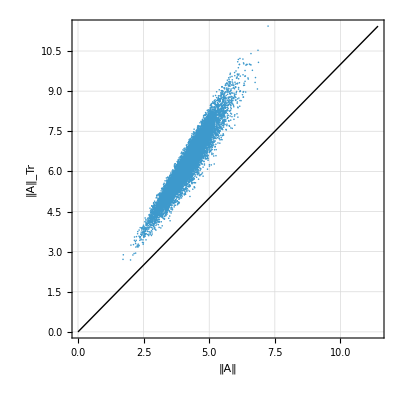

```mathematica
$d=3;
data=Table[
op=RandomMatrix[$d];{HilbertSchmidtNorm[op],TraceNorm[op]},
10000];
max=Max[data];
ListPlot[data,
PlotRange->{{0,1},{0,1}}*max,
Epilog->Line@{{0,0},{1,1}*max},
FrameLabel->{"‖A‖","‖A‖_Tr"},
AspectRatio->1]
```

### Effects of Quantum Noise

One striking difference between the Hilbert-Schmidt and trace norms is the effect of quantum operations. Needless to say, under unitary transformations, both are invariant

(‖U A U^†‖)_HS=(‖A‖)_HS ,        (‖U A U^†‖)_Tr=(‖A‖)_Tr .

However, the norms vary under general quantum operations. Interestingly, a quantum operation F never increases the trace norm

(‖ℱ(A)‖)_Tr≤(‖A‖)_Tr

for any linear operator A. On the contrary, the HilbertSchmidt norm sometimes increases under quantum operations. When applied for the distance measure of quantum states, this behavior has a significant physical implication as we will see soon below. This may give a reason to prefer the trace norm (or distance) to the Hilbert-Schmidt norm (or distance).

In the remainder of this section, we demonstrate the effect of quantum operations on the Hilbert-Schmidt and trace distances.

We define a function to construct the Kraus elements from the unitary representation of the quantum operation. Here U is the unitary operator on the total system (system plus environment) and init is the initial (pure) state of the environment. The system and environment are assumed to be initially in a product state.

```mathematica
$d=3;
Clear[kraus]
kraus[U_?MatrixQ,init_?VectorQ]:=Map[kraus[U,init,#]&,Range[$d]]
kraus[U_?MatrixQ,init_?VectorQ,k_Integer]:=PartialTrace[
U.CircleTimes[One[$d],Dyad[init,UnitVector[$d,k]]],
{$d,$d},{2}];
```

First, we compare the Hilbert-Schmidt norm before and after quantum operations. Sometimes the Hilbert-Schmidt increases after a quantum operation, especially, for operators with large trace.

```mathematica
Timing[
data=Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
mat=RandomReal[{-1,1}]*One[$d]+0.4RandomHermitian[$d];
{HilbertSchmidtNorm[mat],HilbertSchmidtNorm[spr[mat]]},
{10000}
];
]
```

{6.38617,Null}

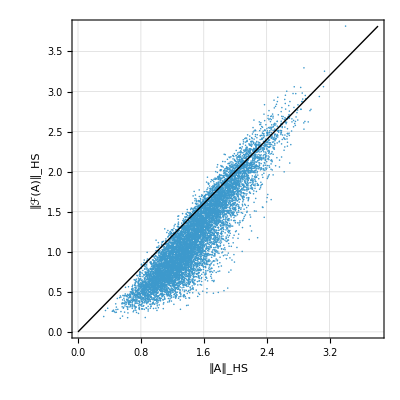

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{0,1},{0,1}}*max,
FrameLabel->{"∥A∥_HS","∥ℱ(A)∥_HS"},
AspectRatio->1]
```

Next, we compare the trace distance before and after quantum operations.

```mathematica
Timing[
data=Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
mat=RandomMatrix[$d];
{TraceNorm[mat],TraceNorm[spr[mat]]},
{10000}
];
]
```

{6.33595,Null}

Unlike the Hilbert-Schmidt norm, the trace norm never increases under a quantum operation.

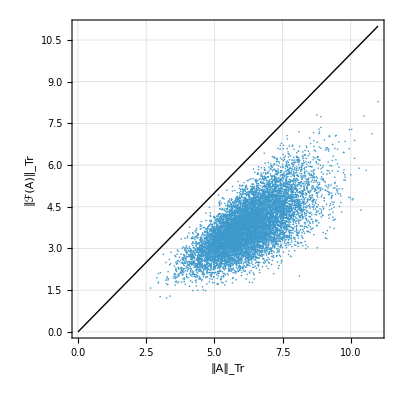

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{0,1},{0,1}}*max,
FrameLabel->{"∥A∥_Tr","∥ℱ(A)∥_Tr"},
AspectRatio->1]
```

Let us further examine more closely the case for traceless Hermitian operators, which are relevant when investigating the trace distances between mixed states.

```mathematica
Timing[
data=Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
mat=RandomHermitian[$d];
mat=mat-Tr[mat]One[$d];
{TraceNorm[mat],TraceNorm[spr[mat]]},
{10000}
];
]
```

{6.46622,Null}

As expected, the trace norm never increases.

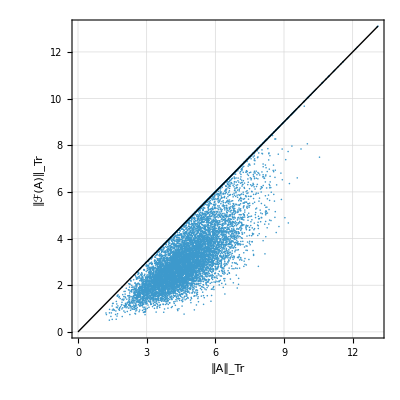

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{0,1},{0,1}}*max,
FrameLabel->{"∥A∥_Tr","∥ℱ(A)∥_Tr"},
AspectRatio->1]
```

Hilbert-Schmidt and Trace Distances

In the above, we have introduced two frequently used operator norms, the Hilbert-Schmidt and trace norms, and discussed their mathematical properties. They naturally provide distance measures, the Hilbert-Schmidt distance

D_HS(A,B):=(‖A-B‖)_HS

and the trace distance

D_Tr(A,B):=(‖A-B‖)_Tr ,

between linear operators on a given vector space. Here we are interested distance measures between quantum states described by density operators, i.e., positive operators with unit trace. Most of the properties of the two distance measures directly follow from those of the corresponding norms. Therefore, here will focus on their physical implications in the context of quantum information.

A stunning property of the trace distance is that it never increases under quantum operations. Suppose that ℱ is a quantum operation. Then, we have

(‖ℱ(A)-ℱ(B)‖)_Tr≤(‖A-B‖)_Tr ,

for any quantum states ρ and σ. Physically, one can regard that a quantum operation causes a loss of some piece of information in quantum states. The loss makes it more difficult to distinguish two quantum states. For an analogy, consider two images. If one blurs the images through image processing, then the resulting images become more similar than the original images. The non-increasing feature of the trace distance under quantum operations has many physical implications and applications. One example is that one can construct an entanglement measure based on the trace distance.

### Relation of the Hilbert-Schmidt Distance to a Classical Distance

The distance measures between quantum states are closely related to the distance measures between classical probability distributions.

Consider the probability distributions {p_m} and {q_m} for two random variables with values in a common set {m}. One way to measure how close they are is to use the Euclidean vector norm

D_E({p_m},{q_m}):=‖p-q‖=√(∑_m (p_m-q_m)^2)

regarding p:=(p_1,p_2,…) and q:=(q_1,q_2,…) as classical Euclidean vectors. To compare it with the Hilbert-Schmidt distance between quantum states, let us consider the probabilities

p_m:=Tr E_m ρ ,    q_m:=Tr E_m σ

associated with a POVM {E_m} measurement on the two quantum states ρ and σ. One can show that

(D_E({p_m},{q_m})≤‖ρ-σ‖)_HS.

Note that the equality holds when the two states ρ and σ commute with each other (i.e., they are diagonalized simultaneously).

The following plot illustrates the relation between the Hilbert-Schmidt distance between quantum states and the vector-norm-based distance between classical probability distributions.

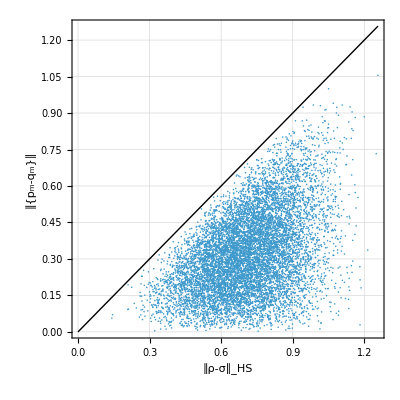

```mathematica
data=Table[
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
pp=Chop@Diagonal[rho];
qq=Chop@Diagonal[sig];
{HilbertSchmidtNorm[rho-sig],Norm[pp-qq]},{10000}];
max=Max[data];
ListPlot[data,PlotRange->{{0,1},{0,1}}*max,Epilog->Line@{{0,0},{1,1}*max},FrameLabel->{"∥ρ-σ∥_HS","∥{p_m-q_m}∥"},AspectRatio->1]
```

### Relation of the Trace Distance to a Classical Distance

On the other hand, the trace distance is the quantum generalization of the so-called Kolmogorov distance

D_K({p_m},{q_m}):=∑_m |p_m-q_m|

between two classical probability distributions {p_m} and {q_m} for two random variables with values in a common set {m}. To see the relation, consider two mixed states ρ and σ and the probability distributions associated with the respective states by

p_m:=Tr E_m ρ ,    q_m:=Tr E_m σ

for a POVM {E_m} measurement on the two quantum states ρ and σ. It turns out that

(D_K({p_m},{q_m})≤‖ρ-σ‖)_Tr.

Equality is attainable by maximizing the distance between probability distributions with an optimal POVM. In other words,

(‖ρ-σ‖)_Tr=max_{E_m} ∑_m|Tr E_m(ρ-σ)|,

where the maximization is over all possible POVM. Since E_m≤I for all POVM elements, one can simplify the above relation and write that

(‖ρ-σ‖)_Tr=max_P Tr P(ρ-σ),

where the maximization is over all positive operators P such that P≤I.

The following plot demonstrate the relation between the trace distance between quantum states and the Kolmogorov distance between classical probability distributions.

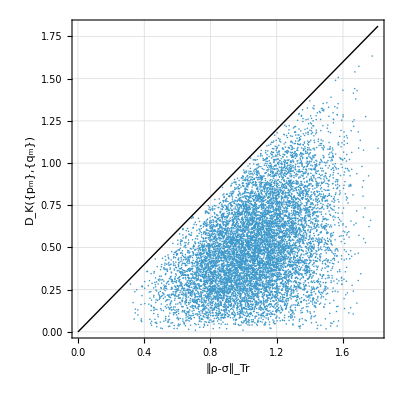

```mathematica
data=Table[
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
pp=Chop@Diagonal[rho];
qq=Chop@Diagonal[sig];
{TraceNorm[rho-sig],Total@Abs[pp-qq]},{10000}];
max=Max[data];
ListPlot[data,PlotRange->{{0,1},{0,1}}*max,Epilog->Line@{{0,0},{1,1}*max},FrameLabel->{"∥ρ-σ∥_Tr","D_K({p_m},{q_m})"},AspectRatio->1]
```

Fidelity

We have discussed two norm-derived distance measures. Fidelity is another frequently used measure of the closeness of quantum states. Unlike the Hermitian and trace distances, it is not based on a norm. Rather, conceptually it is similar to the relative “angle” between the two quantum states. Since quantum states are normalized, it seems natural to expect closer quantum states to have a smaller relative angle. The fidelity is the quantum generalization of the (classical) fidelity between two probability distributions.

For two quantum states described by density operators ρ and σ, the fidelity between them is defined by

F(ρ,σ):=Tr √(√ρ σ √ρ).

At first glance, the above definition looks asymmetric for the two states, but the fidelity is actually symmetric. One way to see this is to express the fidelity in terms of the trace distance discussed above, that is,

F(ρ,σ)=(‖√ρ √σ‖)_Tr .

Although the fidelity is not derived from a norm, it is invariant under unitary transformations

F(U ρ U^†,U σ U^†)=F(ρ,σ) .

One can see this by recalling that for any positive operator A, the square-root function is homomorphic under unitary transformations, √(U A U^†)=U √A U^†.

When one or both of the two states are pure states, the expression for the fidelity gets simpler,

F(vv,ρ)=√vρv

and

F(vv,ww)=|vw| .

The above two limiting cases clearly indicate that geometrically, the fidelity is an extension of the relative “angle”. For an analogy, recall that in the three-dimensional Euclidean space, the inner product of two vectors normalized vectors a and b (∥a∥ = ∥b∥ = 1) is given by a·b=cos(θ).

For quantum states, parallel and anti-parallel arrangements are not distinguished. Consequently, we expect the fidelity to be 1 for identical states, ρ=σ, which is indeed true. Below, we will see that the fidelity is bounded between 0 and 1,

0≤F(ρ,σ)≤1

for any states ρ and σ, and F(ρ,σ)=1 if and only if ρ=σ. That is, the fidelity approaches 1 for closer quantum states and decreases for more different quantum states.

### Uhlmann’s Theorem

The most fundamental property of the fidelity is Uhlmann’s theorem. Suppose that Ψ and Φ are the purifications of ρ and σ, respectively, into 𝒱⊗ℰ with dim ℰ=dim 𝒱, that is,

ρ=Tr_ℰ ΨΨ ,    σ=Tr_ℰ ΦΦ.

Uhlmann’s theorem states that the fidelity between ρ and σ cannot be smaller than the fidelity between the purifications Ψ and Φ,

F(ρ,σ)≥|ΨΦ| .

The bound is optimal in the sense that there always exists an optimal purification attaining equality. Putting it another way,

F(ρ,σ)=max_{Ψ,Φ} |ΨΦ|,

where the maximization is over all possible purifications of ρ and σ.

Uhlmann’s theorem is not particularly useful for specific calculations of the fidelity. However, as we will see below, many properties of the fidelity can be assessed more conveniently by employing Uhlmann’s theorem than the defining expression.

As an example of the application of Uhlmann’s theorem, we note that the bounds of the fidelity,

0≤F(ρ,σ)≤1

follow immediately from Uhlmann’s theorem. One can further examine when the fidelity attains F(ρ,σ)=1. If ρ= σ, then it is obvious that F(ρ,σ)=1. To prove the converse, suppose that ρ≠σ. Then, Ψ≠Φ for any purifications Ψ and Φ of ρ and σ, respectively. Therefore, the fidelity must be strictly less than unity, F(ρ, σ)<1, contradicting the assumption. Thus we have shown that F(ρ, σ)=1 if and only if ρ=σ.

### Effects of Quantum Noise

Similar to the non-increasing feature of the trace distance, the fidelity never decreases under quantum operations. In other words,

F(ℱ(ρ),ℱ(σ))≥F(ρ,σ)

for any quantum operation ℱ and quantum states ρ and σ on a vector space 𝒱.

The interpretation of the above inequality is the same as for the trace distance. The "damage" due to the quantum operation makes the resulting two states look more similar than the original quantum states.

The above inequality can be proved by using Uhlmann’s theorem.

The following plot illustrates the non-decreasing feature of the fidelity under quantum operations.

```mathematica
Timing[
$d=3;
Clear[kraus];
kraus[U_?MatrixQ,init_?VectorQ]:=Map[kraus[U,init,#]&,Range[$d]];
kraus[U_?MatrixQ,init_?VectorQ,k_Integer]:=PartialTrace[
U.CircleTimes[One[$d],Dyad[init,UnitVector[$d,k]]],
{$d,$d},{2}];
data=Chop@Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
{Fidelity[rho,sig],Fidelity[spr[rho],spr[sig]]},
{10000}
];
]
```

{8.65557,Null}

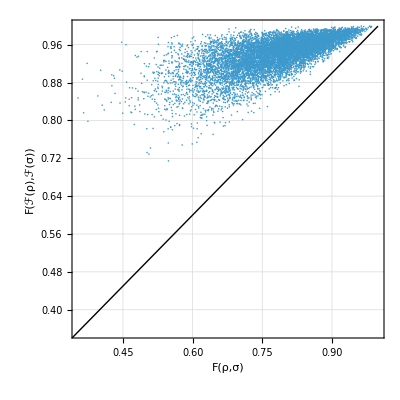

```mathematica
max=Max[data];
min=Min[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{min,max},{min,max}},
FrameLabel->{"F(ρ,σ)","F(ℱ(ρ),ℱ(σ))"},
AspectRatio->1]
```

### Relation to the Classical Fidelity

The fidelity for two quantum states is a natural generalization of the fidelity between two classical probability distributions. To examine the relation, consider a POVM {E_m} and the corresponding probability distributions

p_m:=Tr E_m ρ ,     q_m:=Tr E_m σ

associated with two quantum states ρ and σ. One can show that

F(ρ,σ)≤F_cl({p_m},{q_m}) .

A proof is given in Problem 5.15 in the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7.

The following plot illustrates the above relation between the fidelity of quantum states and the fidelity of classical probability distributions.

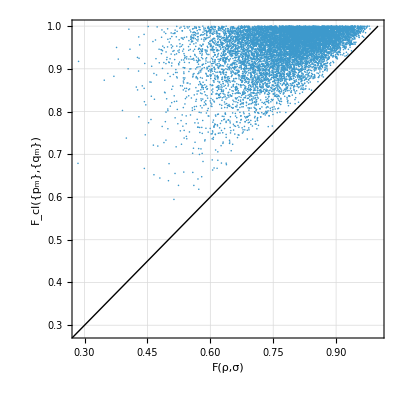

```mathematica
data=Chop@Table[
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
pp=Chop@Diagonal[rho];
qq=Chop@Diagonal[sig];
{Fidelity[rho,sig],Total@Sqrt[pp*qq]},{10000}];
min=Min[data];
max=Max[data];
ListPlot[data,PlotRange->{{min,max},{min,max}},Epilog->Line@{{0,0},{1,1}*max},FrameLabel->{"F(ρ,σ)","F_cl({p_m},{q_m})"},AspectRatio->1]
```

| Related Guides
▪Quantum Information Systems
▪Distance and Similarity Measures

| Related Tech Notes
▪Quantum Noise and Decoherence
▪Quantum Information Theory
▪Quantum Information Systems with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).